```mathematica
Integrate[Exp[2 Pi I p q]Exp[I Pi τ p^2],{p,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-(ⅈ π q^2)/τ))/(√(-ⅈ τ)),Im[τ]>0]

```mathematica
Integrate[Exp[2 Pi I p q]Exp[-I Pi p^2/τ],{p,-Infinity,Infinity}]
```

ConditionalExpression[ⅇ^(ⅈ π q^2 τ) √(-ⅈ τ),Im[τ]>0]

```mathematica
D[1/w Sum[(w/z)^(n+k/L),{n,0,Infinity}],z]//Simplify
```

-((w/z)^(k/L) (L w+k (-w+z)))/(L w (w-z)^2)

```mathematica
(Series[-((w/z)^(k/L) (L w+k (-w+z)))/(L w (w-z)^2),{w,z,0}]//Normal)/.k->L/2
```

-1/(w-z)^2-1/(8 z^2)

```mathematica
Sum[1/n^2 Exp[2 Pi I n s],{n,1,Infinity}]
```

PolyLog[2,ⅇ^(2 ⅈ π s)]

```mathematica
Assuming[0.1>s>0,Series[PolyLog[2,ⅇ^(2 ⅈ π s)]+PolyLog[2,ⅇ^(-2 ⅈ π s)],{s,0,1}]]
```

Floor[Arg[ⅇ^(-2 ⅈ π s) (-1+ⅇ^(2 ⅈ π s)-2 ⅈ ⅇ^(2 ⅈ π s) π s)]/(2 π)] (2 ⅈ π Log[-ⅈ/(2 π)] s+O[s]^2)+Floor[Arg[1-ⅇ^(2 ⅈ π s)+2 ⅈ π s]/(2 π)] (-2 ⅈ π Log[ⅈ/(2 π)] s+O[s]^2)+Floor[Arg[1-ⅇ^(2 ⅈ π s)+2 ⅈ π s]/(2 π)] (-2 ⅈ π Log[-2 ⅈ π] s+O[s]^2)+Floor[Arg[ⅇ^(-2 ⅈ π s) (-1+ⅇ^(2 ⅈ π s)-2 ⅈ ⅇ^(2 ⅈ π s) π s)]/(2 π)] (2 ⅈ π Log[2 ⅈ π] s+O[s]^2)+(π^2/3-2 ⅈ (π Log[-2 ⅈ π]-π Log[2 ⅈ π]) s+O[s]^2)

```mathematica
((n+3)(n+2))/2+((n)(n-1))/2-n(n+3)//Simplify
```

3-n

```mathematica
Series[Gamma[-1-l^2 s/4]/Gamma[2+l^2 s/4],{s,-4/l^2,0}]
```

-4/(l^2 (s+4/l^2))-2 EulerGamma+O[s+4/l^2]^1

```mathematica
Series[Gamma[-1-l^2 s/4]/Gamma[2+l^2 s/4],{s,0,0}]
```

4/(l^2 s)+2 (-1+EulerGamma)+O[s]^1

```mathematica
Series[Gamma[-1-l^2 u/4]/Gamma[2+l^2 u/4] Gamma[-1-l^2 t/4]/Gamma[2+l^2 t/4] Gamma[-1-l^2 s/4]/Gamma[2+l^2 s/4],{s,0,-1}]//Normal
```

```mathematica
(4 Gamma[-1-(l^2 t)/4] Gamma[-1-(l^2 u)/4])/(l^2 s Gamma[2+(l^2 t)/4] Gamma[2+(l^2 u)/4])/.u->-16/l^2-t//Simplify
```

(4 Gamma[-1-(l^2 t)/4] Gamma[3+(l^2 t)/4])/(l^2 s Gamma[-2-(l^2 t)/4] Gamma[2+(l^2 t)/4])

```mathematica
-4/(l^2 s (1+(l^2 t)/4 )(1+(l^2 t)/4))
```

```mathematica
(Gamma[-1-(l^2 t)/4] Gamma[-1-(l^2 u)/4])/(Gamma[2+(l^2 t)/4] Gamma[2+(l^2 u)/4])//Simplify
```

(Gamma[-1-(l^2 t)/4] Gamma[-1-(l^2 u)/4])/(Gamma[2+(l^2 t)/4] Gamma[2+(l^2 u)/4])

```mathematica
Integrate[Exp[-1/2 a x^2+I b x],{x,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-b^2/(2 a)) √(2 π))/(√a),Re[a]>0]

```mathematica
K1=-(k2a+k3a/z);
K2=k1b+k4b/(1-z);
K3=(1+z)k1c+z k2c+k4c;
K4=k1d/z+k2d/(z-1);
K3 K4+K1 K2+K1 K4+1/z^2 K2 K3+K2 K4+1/(1-z)^2 K1 K3
```

(k1b+k4b/(1-z)) (k2d/(-1+z)+k1d/z)+(k1b+k4b/(1-z)) (-k2a-k3a/z)+(k2d/(-1+z)+k1d/z) (-k2a-k3a/z)+(k2d/(-1+z)+k1d/z) (k4c+k2c z+k1c (1+z))+((-k2a-k3a/z) (k4c+k2c z+k1c (1+z)))/(1-z)^2+((k1b+k4b/(1-z)) (k4c+k2c z+k1c (1+z)))/z^2

```mathematica
K1 K2 K3 K4//FullSimplify
```

((k1b+k4b-k1b z) (k3a+k2a z) (k1c+k4c+(k1c+k2c) z) (k1d (-1+z)+k2d z))/((-1+z)^2 z^2)

```mathematica
FactorInteger[8192]
```

{{2,13}}

```mathematica
Integrate[(1+w^2)^(-1-α),{w,-Infinity,Infinity}]
```

ConditionalExpression[(√π Gamma[1/2+α])/Gamma[1+α],Re[α]>-1/2]

```mathematica
(z-I)/(z+I)-(w-I)/(w+I)
```

```mathematica
Integrate[((1-Cos[θ])^2+Sin[θ]^2)^α,{θ,0,2Pi}]
```

ConditionalExpression[(2^(1+2 α) √π Gamma[1/2+α])/Gamma[1+α],Re[α]>-1/2]

```mathematica
(2^(1+2 α) √π Gamma[1/2+α])/Gamma[1+α]//FullSimplify
```

(2^(1+2 α) √π Gamma[1/2+α])/Gamma[1+α]

```mathematica
(√π Gamma[-1/2-α])/Gamma[-α]/.α->(-1-α)
```

(√π Gamma[1/2+α])/Gamma[1+α]

```mathematica
Solve[w==(z-I)/(z+I),z]
```

{{z→-(ⅈ (1+w))/(-1+w)}}

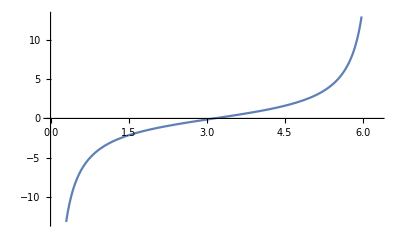

```mathematica
Plot[(-4 Sin[θ])/((1-Exp[I θ]) (1-Exp[-I θ])),{θ,0,2Pi}]
```

```mathematica
D[(-4 Sin[θ])/((1-Exp[I θ]) (1-Exp[-I θ])),θ]//Simplify
```

-(4 ⅇ^(ⅈ θ))/((-1+ⅇ^(ⅈ θ))^2)

```mathematica
Simplify[(I(1+z)/(1-z)-I(1+w)/(1-w))(-I(1+zb)/(1-zb)-(-I)(1+wb)/(1-wb))(I(1+z)/(1-z)-(-I)(1+wb)/(1-wb))((-I)(1+zb)/(1-zb)-I(1+w)/(1-w))]
```

(16 (w-z) (-1+wb z) (wb-zb) (-1+w zb))/((-1+w)^2 (-1+wb)^2 (-1+z)^2 (-1+zb)^2)

```mathematica
Simplify[((z-I)/(z+I)-(w-I)/(w+I))((zb+I)/(zb-I)-(wb+I)/(wb-I))]
```

(4 (w-z) (wb-zb))/((ⅈ+w) (-ⅈ+wb) (ⅈ+z) (-ⅈ+zb))

```mathematica
Integrate[r^(1-α)(1+r^2)^(α/2),{r,0,1}]
```

ConditionalExpression[-1/2 ⅈ^α Beta[-1,1-α/2,1+α/2],Re[α]<2]

```mathematica
-1/2 ⅈ^α Beta[-1,1-α/2,1+α/2]//FullSimplify
```

-1/2 ⅈ^α Beta[-1,1-α/2,1+α/2]

```mathematica
Integrate[w^α(1-w)^β,{w,0,1}]
```

ConditionalExpression[(Gamma[1+α] Gamma[1+β])/Gamma[2+α+β],Re[α]>-1&&Re[β]>-1]

```mathematica
Integrate[w^(-u-2)(1-w)^(-t-2),{w,0,1}]
Integrate[w^(-u-2)(1+w)^(-t-2),{w,0,Infinity}]
Integrate[w^(-u-2)(w-1)^(-t-2),{w,1,Infinity}]
```

ConditionalExpression[(Gamma[-1-t] Gamma[-1-u])/Gamma[-2-t-u],Re[t]<-1&&Re[u]<-1]

ConditionalExpression[(Gamma[-1-u] Gamma[3+t+u])/Gamma[2+t],Re[u]<-1&&Re[t+u]>-3]

ConditionalExpression[(Gamma[-1-t] Gamma[3+t+u])/Gamma[2+u],Re[t]<-1&&Re[u]<-1&&Re[t+u]>-3]

```mathematica
Integrate[w^-u(1-w)^-t,{w,0,1}]
Integrate[w^-u(1+w)^-t,{w,0,Infinity}]
Integrate[w^-u(w-1)^-t,{w,1,Infinity}]
```

ConditionalExpression[(Gamma[1-t] Gamma[1-u])/Gamma[2-t-u],Re[t]<1&&Re[u]<1]

ConditionalExpression[(Gamma[1-u] Gamma[-1+t+u])/Gamma[t],Re[u]<1&&Re[t+u]>1]

ConditionalExpression[(Gamma[1-t] Gamma[-1+t+u])/Gamma[u],Re[t]<1&&Re[u]<1&&Re[t+u]>1]

```mathematica
Series[Series[(Gamma[1-t] Gamma[1-u])/Gamma[2-t-u],{t,0,0}]//Normal,{u,0,1}]
Series[(Gamma[1-u] Gamma[-1+t+u])/Gamma[t],{t,0,0}]
Series[Series[(Gamma[1-t] Gamma[-1+t+u])/Gamma[u],{t,0,0}]//Normal,{u,0,1}]
```

1+u+O[u]^2

O[t]^1

-1-u+O[u]^2

```mathematica
Gamma[-1/2 +2]/Gamma[2]//Simplify
```

(√π)/2

```mathematica
Integrate[(x^2+1)^α,{x,-Infinity,Infinity}]
```

ConditionalExpression[(√π Gamma[-1/2-α])/Gamma[-α],Re[α]<-1/2]

```mathematica
Integrate[y^-u(1-y)^-t,{y,0,1}]
Integrate[y^(-u-2)(1-y)^-t,{y,0,1}]
Integrate[y^-u(1-y)^(-t-2),{y,0,1}]
```

ConditionalExpression[(Gamma[1-t] Gamma[1-u])/Gamma[2-t-u],Re[t]<1&&Re[u]<1]

ConditionalExpression[(Gamma[1-t] Gamma[-1-u])/Gamma[-t-u],Re[t]<1&&Re[u]<-1]

ConditionalExpression[(Gamma[-1-t] Gamma[1-u])/Gamma[-t-u],Re[t]<-1&&Re[u]<1]

```mathematica
Integrate[y^-u(1+y)^-t,{y,0,Infinity}]
Integrate[y^(-u-2)(1+y)^-t,{y,0,Infinity}]
Integrate[y^-u(1+y)^(-t-2),{y,0,Infinity}]
```

ConditionalExpression[(Gamma[1-u] Gamma[-1+t+u])/Gamma[t],Re[u]<1&&Re[t+u]>1]

ConditionalExpression[(Gamma[-1-u] Gamma[1+t+u])/Gamma[t],Re[u]<-1&&Re[t+u]>-1]

ConditionalExpression[(Gamma[1-u] Gamma[1+t+u])/Gamma[2+t],Re[u]<1&&Re[t+u]>-1]

```mathematica
Integrate[y^-u(-1+y)^-t,{y,1,Infinity}]
Integrate[y^(-u-2)(-1+y)^-t,{y,1,Infinity}]
Integrate[y^-u(-1+y)^(-t-2),{y,1,Infinity}]
```

ConditionalExpression[(Gamma[1-t] Gamma[-1+t+u])/Gamma[u],Re[t]<1&&Re[u]<1&&Re[t+u]>1]

ConditionalExpression[(Gamma[1-t] Gamma[1+t+u])/Gamma[2+u],Re[t]<1&&Re[u]<-1&&Re[t+u]>-1]

ConditionalExpression[(Gamma[-1-t] Gamma[1+t+u])/Gamma[u],Re[t]<-1&&Re[u]<1&&Re[t+u]>-1]

```mathematica
Integrate[y^-u(1+y)^-t (-1+y)/y,{y,0,Infinity}]
Integrate[y^-u(1-y)^-t (1+y)/y,{y,0,1}]
Integrate[y^-u(y-1)^-t (1+y)/y,{y,1,Infinity}]
```

ConditionalExpression[-((-1+t+2 u) Gamma[-u] Gamma[-1+t+u])/Gamma[t],Re[u]<0&&Re[t+u]>1]

ConditionalExpression[(t (-1+t+2 u) Gamma[-t] Gamma[-u])/Gamma[2-t-u],Re[t]<1&&Re[u]<0]

ConditionalExpression[((-1+t+2 u) Gamma[1-t] Gamma[-1+t+u])/Gamma[1+u],Re[t]<1&&Re[u]<1&&Re[t+u]>1]

```mathematica
Integrate[y^-u(1+y)^-t (-1+y)/(y+1),{y,0,Infinity}]
Integrate[y^-u(1-y)^-t (1+y)/(y-1),{y,0,1}]
Integrate[y^-u(y-1)^-t (1+y)/(y-1),{y,1,Infinity}]
```

ConditionalExpression[(u (-2+t+2 u) Gamma[-u] Gamma[-1+t+u])/Gamma[1+t],Re[u]<1&&Re[t+u]>1]

ConditionalExpression[-(u (-2+t+2 u) Gamma[-t] Gamma[-u])/Gamma[2-t-u],Re[t]<0&&Re[u]<1]

ConditionalExpression[((-2+t+2 u) Gamma[-t] Gamma[-1+t+u])/Gamma[u],Re[t]<0&&Re[u]<2&&Re[t+u]>1]

```mathematica
((-1+t+2 u) Gamma[1-t] Gamma[-1+t+u])/Gamma[1+u]+(t (-1+t+2 u) Gamma[-t] Gamma[-u])/Gamma[2-t-u]-((-1+t+2 u) Gamma[-u] Gamma[-1+t+u])/Gamma[t]+(u (-2+t+2 u) Gamma[-u] Gamma[-1+t+u])/Gamma[1+t]-(u (-2+t+2 u) Gamma[-t] Gamma[-u])/Gamma[2-t-u]+((-2+t+2 u) Gamma[-t] Gamma[-1+t+u])/Gamma[u]//Simplify
```

```mathematica
((-2+u-s) Gamma[-t] Gamma[1-u])/Gamma[2+s]+((-1+u-s) Gamma[1-t] Gamma[-u])/Gamma[2+s]-((-1+u-s) Gamma[-u] Gamma[-1-s])/Gamma[t]+((-2+u-s) Gamma[1-u] Gamma[-1-s])/Gamma[1+t]+((-2+u-s) Gamma[-t] Gamma[-1-s])/Gamma[u]+((-1+u-s) Gamma[1-t] Gamma[-1-s])/Gamma[1+u]
```

```mathematica
-(((1+s)+(1-u)) Gamma[-t] Gamma[1-u])/((1+s)Gamma[1+s])+((-1+u-s) Gamma[1-t] Gamma[-u])/Gamma[2+s]-((-1+u-s) Gamma[-u] Gamma[-1-s])/Gamma[t]+((-2+u-s) Gamma[1-u] Gamma[-1-s])/Gamma[1+t]+((-2+u-s) Gamma[-t] Gamma[-1-s])/Gamma[u]+((-1+u-s) Gamma[1-t] Gamma[-1-s])/Gamma[1+u]
```

```mathematica
(*s-sector*)
-(Gamma[-t] Gamma[1-u])/Gamma[1+s]-(Gamma[-t] Gamma[2-u])/Gamma[2+s]-(Gamma[1-t] Gamma[-u])/Gamma[1+s]-(Gamma[1-t] Gamma[1-u])/Gamma[2+s]
```

```mathematica
(*t-sector*)
-(Gamma[1-u] Gamma[-1-s])/Gamma[t]-(Gamma[-u] Gamma[-s])/Gamma[t]-(Gamma[2-u] Gamma[-1-s])/Gamma[1+t]+(Gamma[1-u] Gamma[-s])/Gamma[1+t]
```

```mathematica
(*u-sector*)
(Gamma[-t] Gamma[-1-s])/Gamma[u-1]+(Gamma[-t] Gamma[-s])/Gamma[u]+(Gamma[1-t] Gamma[-1-s])/Gamma[u]+(Gamma[1-t] Gamma[-s])/Gamma[1+u]
```

```mathematica
Integrate[y^-u(1+y)^-t,{y,0,Infinity}]
Integrate[y^-u(1-y)^-t,{y,0,1}]
Integrate[y^-u(y-1)^-t ,{y,1,Infinity}]
```

ConditionalExpression[(Gamma[1-u] Gamma[-1+t+u])/Gamma[t],Re[u]<1&&Re[t+u]>1]

ConditionalExpression[(Gamma[1-t] Gamma[1-u])/Gamma[2-t-u],Re[t]<1&&Re[u]<1]

ConditionalExpression[(Gamma[1-t] Gamma[-1+t+u])/Gamma[u],Re[t]<1&&Re[u]<1&&Re[t+u]>1]

```mathematica
Integrate[y^-u(1+y)^-t (-y),{y,0,Infinity}]
Integrate[y^-u(1-y)^-t y,{y,0,1}]
Integrate[y^-u(y-1)^-t y ,{y,1,Infinity}]
```

ConditionalExpression[-(Gamma[2-u] Gamma[-2+t+u])/Gamma[t],Re[u]<2&&Re[t+u]>2]

ConditionalExpression[(Gamma[1-t] Gamma[2-u])/Gamma[3-t-u],Re[t]<1&&Re[u]<2]

ConditionalExpression[(Gamma[1-t] Gamma[-2+t+u])/Gamma[-1+u],Re[t]<1&&Re[u]<2&&Re[t+u]>2]

```mathematica
Integrate[y^-u(1+y)^-t (1+y),{y,0,Infinity}]
Integrate[y^-u(1-y)^-t(y-1),{y,0,1}]
Integrate[y^-u(y-1)^-t(y-1) ,{y,1,Infinity}]
```

ConditionalExpression[(Gamma[1-u] Gamma[-2+t+u])/Gamma[-1+t],Re[u]<1&&Re[t+u]>2]

ConditionalExpression[-(Gamma[2-t] Gamma[1-u])/Gamma[3-t-u],Re[t]<2&&Re[u]<1]

ConditionalExpression[(Gamma[2-t] Gamma[-2+t+u])/Gamma[u],Re[t]<2&&Re[u]<1&&Re[t+u]>2]

```mathematica
Integrate[y^-u(1+y)^-t (1+y)(-y),{y,0,Infinity}]
Integrate[y^-u(1-y)^-t(y-1)y,{y,0,1}]
Integrate[y^-u(y-1)^-t(y-1) y,{y,1,Infinity}]
```

ConditionalExpression[-(Gamma[2-u] Gamma[-3+t+u])/Gamma[-1+t],Re[u]<2&&Re[t+u]>3]

ConditionalExpression[-(Gamma[2-t] Gamma[2-u])/Gamma[4-t-u],Re[t]<2&&Re[u]<2]

ConditionalExpression[(Gamma[2-t] Gamma[-3+t+u])/Gamma[-1+u],Re[t]<2&&Re[u]<2&&Re[t+u]>3]

```mathematica
Gamma[-1/2+2]/Gamma[2]
```

(√π)/2

```mathematica
Integrate[(1+w^2)^α,{w,-Infinity,Infinity}]
```

ConditionalExpression[(√π Gamma[-1/2-α])/Gamma[-α],Re[α]<-1/2]

```mathematica
Integrate[r^(-4+1)(1+r^2)^(4/2),{r,0,1}]
```

∫_0^1 ((1+r^2)^2)/r^3 ⅆr

```mathematica
Series[-1/2 ⅈ^α Beta[-1,1-α/2,1+α/2],{α,4,0}]
```

Beta[-1,1-α/2,1+α/2] (-1/2+O[α-4]^1)

```mathematica
Series[1/2 Log[p^2+m^2],{p,0,6}]
```

Log[m^2]/2+p^2/(2 m^2)-p^4/(4 m^4)+p^6/(6 m^6)+O[p]^7

```mathematica
Integrate[1/t^(1-ϵ)Exp[-2 Pi t S],{t,0,Infinity}]
```

ConditionalExpression[(2 π)^-ϵ S^-ϵ Gamma[ϵ],Re[S]>0&&Re[ϵ]>0]

```mathematica
-Series[(2 π)^-ϵ S^-ϵ Gamma[ϵ+1],{ϵ,0,1}]
```

-1+(EulerGamma+Log[2 π]+Log[S]) ϵ+O[ϵ]^2

```mathematica
(2Pi)^EulerGamma//N
```

2.88883

```mathematica
Integrate[2 Sin[ψ]^2,{ψ,0,Pi}]
Integrate[Sin[θ],{θ,0,Pi}]
```

π

2

```mathematica
InverseMetric[g_]:=Simplify[Inverse[g]]
ChristoffelSymbol[g_,xx_]:=Block[{n,ig,res},n=Length[g];
ig=InverseMetric[g];
res=Table[(1/2)*Sum[ig[[i,s]]*(-D[g[[j,k]],xx[[s]]]+D[g[[j,s]],xx[[k]]]+D[g[[s,k]],xx[[j]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}];
Simplify[res]]
RiemannTensor[g_,xx_]:=Block[{n,Chr,res},n=Length[g];
Chr=ChristoffelSymbol[g,xx];
res=Table[D[Chr[[i,k,m]],xx[[l]]]-D[Chr[[i,k,l]],xx[[m]]]+Sum[Chr[[i,s,l]]*Chr[[s,k,m]],{s,1,n}]-Sum[Chr[[i,s,m]]*Chr[[s,k,l]],{s,1,n}],{i,1,n},{k,1,n},{l,1,n},{m,1,n}];
Simplify[res]]
RicciTensor[g_,xx_]:=Block[{Rie,res,n},n=Length[g];
Rie=RiemannTensor[g,xx];
res=Table[Sum[Rie[[s,i,s,j]],{s,1,n}],{i,1,n},{j,1,n}];
Simplify[res]]
RicciScalar[g_,xx_]:=Block[{Ricc,ig,res,n},n=Length[g];Ricc=RicciTensor[g,xx];ig=InverseMetric[g];
res=Sum[ig[[s,i]] Ricc[[s,i]],{s,1,n},{i,1,n}];
Simplify[res]]
```

```mathematica
g=R^2({{1, 0, 0}, {0, Sin[ψ]^2, 0}, {0, 0, Sin[ψ]^2 Sin[θ]^2}});
ginv=InverseMetric[g];
xx={ψ,θ,ϕ};
RicciTensor[g,xx]
RicciScalar[g,xx]
```

{{2,0,0},{0,2 Sin[ψ]^2,0},{0,0,2 Sin[θ]^2 Sin[ψ]^2}}

6/R^2

```mathematica
g=({{F[ϕ], 0, 0, 0}, {0, ϕ R^2, 0, 0}, {0, 0, ϕ R^2 Sin[ψ]^2, 0}, {0, 0, 0, ϕ R^2 Sin[ψ]^2 Sin[θ]^2}});
ginv=InverseMetric[g];
xx={ϕ,ψ,θ,ϕ2};
RicciTensor[g,xx]//MatrixForm
```

((3 (F[ϕ]+ϕ F'[ϕ]))/(4 ϕ^2 F[ϕ]) | 0 | 0 | 0
0 | 1/4 (8-R^2/(ϕ F[ϕ])+(R^2 F'[ϕ])/F[ϕ]^2) | 0 | 0
0 | 0 | (Sin[ψ]^2 (-R^2 F[ϕ]+8 ϕ F[ϕ]^2+R^2 ϕ F'[ϕ]))/(4 ϕ F[ϕ]^2) | 0
0 | 0 | 0 | (Sin[θ]^2 Sin[ψ]^2 (-R^2 F[ϕ]+8 ϕ F[ϕ]^2+R^2 ϕ F'[ϕ]))/(4 ϕ F[ϕ]^2))

```mathematica
DSolve[-R^2 F[ϕ]+8 ϕ F[ϕ]^2+R^2 ϕ F'[ϕ]==0,F,ϕ]
```

```mathematica
(3 (F[ϕ]+ϕ F'[ϕ]))/(4 ϕ^2 F[ϕ]({{0, 0}, {0, 0}}))/.{{F->Function[{ϕ},(R^2 ϕ)/(4 ϕ^2+R^2 C[1])]}}//Simplify
```

{(3 R^2 C[1])/(8 ϕ^4+2 R^2 ϕ^2 C[1])}

```mathematica
g=({{R^2/(4 ϕ), 0, 0, 0}, {0, ϕ R^2, 0, 0}, {0, 0, ϕ R^2 Sin[ψ]^2, 0}, {0, 0, 0, ϕ R^2 Sin[ψ]^2 Sin[θ]^2}});
xx={ϕ,ψ,θ,ϕ2};
RicciTensor[g,xx]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
H123=2 R^2 Sin[ψ]^2 Sin[θ]
2ginv⟦2,2⟧ginv⟦3,3⟧ H123 H123
2ginv⟦1,1⟧ginv⟦3,3⟧ H123 H123 
2ginv⟦1,1⟧ginv⟦2,2⟧ H123 H123
```

```mathematica
g=({{gtt[t], 0}, {0, gxx[t]}});
xx={t,x};
RicciTensor[g,xx]//Simplify
```

{{(gxx[t] gtt'[t] gxx'[t]+gtt[t] gxx'[t]^2-2 gtt[t] gxx[t] gxx''[t])/(4 gtt[t] gxx[t]^2),0},{0,(gxx[t] gtt'[t] gxx'[t]+gtt[t] gxx'[t]^2-2 gtt[t] gxx[t] gxx''[t])/(4 gtt[t]^2 gxx[t])}}

```mathematica
(gxx[t] gtt'[t] gxx'[t]+gtt[t] gxx'[t]^2-2 gtt[t] gxx[t] gxx''[t])/(4 gtt[t]^2 gxx[t]^2)
```

(gxx[t] gtt'[t] gxx'[t]+gtt[t] gxx'[t]^2-2 gtt[t] gxx[t] gxx''[t])/(4 gtt[t]^2 gxx[t]^2)

```mathematica
(-2 gtx[t] gtx'[t] gxx'[t]+gtt[t] gxx'[t]^2+2 gtx[t]^2 gxx''[t]+gxx[t] (gtt'[t] gxx'[t]-2 gtt[t] gxx''[t]))
```

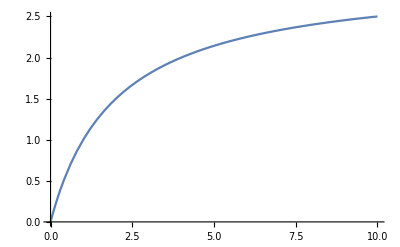

```mathematica
Plot[3k/(k+2),{k,0,10}]
```

```mathematica
Solve[p^2/4+1==1/24(d-1),p]
```

{{p→-(√(-25+d))/(√6)},{p→(√(-25+d))/(√6)}}

```mathematica
Integrate[Exp[R^2/(4 Pi α)A^2-I/(2Pi)A dϕ],{A,-Infinity,Infinity}]
```

ConditionalExpression[(2 ⅇ^((dϕ^2 α)/(4 π R^2)) π)/(√(-R^2/α)),Re[R^2/α]<0]

```mathematica
Integrate[Exp[-1/(4 Pi)A^2+I/(2Pi)A dϕ],{A,-Infinity,Infinity}]
```

2 ⅇ^(-dϕ^2/(4 π)) π

```mathematica
Exp[Log[2 Pi ls/R] Zeta[0]]
```

1/(√(2 π) √(ls/R))

```mathematica
Zeta[0]
```

-1/2

```mathematica
1+Binomial[8,2]+Binomial[8,4]/2
Binomial[8,1]+Binomial[8,3]
```

64

64

```mathematica
8 2^(10/2-1)
```

128

```mathematica
Simplify[((d-2)(d-1))/2-1]
```

1/2 (-3+d) d

```mathematica
Solve[D[n/x+x/n,x]==0]
```

{{x→-n},{x→n}}

```mathematica
n/x+x/n/.x->n
```

2

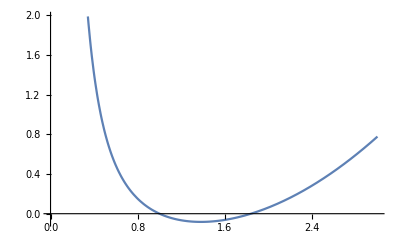

```mathematica
Plot[1/4(1/x^2+x^2-2x),{x,0,3}]
```

```mathematica
Solve[1/4(1/x^2+x^2+2re)==1,re]
```

{{re→(-1+4 x^2-x^4)/(2 x^2)}}

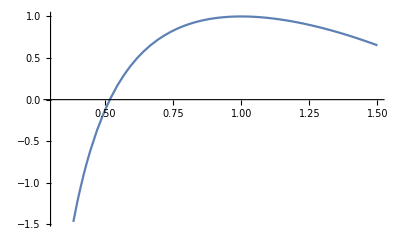

```mathematica
Plot[(-1+4 x^2-x^4)/(2 x^2),{x,0.3,1.5}]
```

```mathematica
(-1+4 x^2-x^4)/(2 x^2) 1/(2x)+x/2//Simplify
```

(-1+4 x^2+x^4)/(4 x^3)

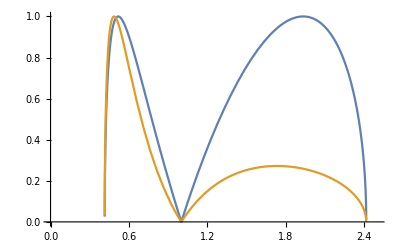

```mathematica
Plot[{Sqrt[1-((-1+4 x^2-x^4)/(2 x^2))^2]  ,Sqrt[1-((-1+4 x^2+x^4)/(4 x^3))^2]},{x,0,2.5}]
```

```mathematica
Solve[(2x)^2+(x^2)^2-4rz x^3==1,rz]
```

{{rz→(-1+4 x^2+x^4)/(4 x^3)}}

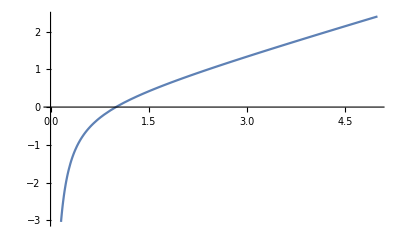

```mathematica
Plot[-1/(2x)+x/2,{x,0,5}]
```

```mathematica
Solve[2^12==n+n^2/2^14,n]
```